## SOM, no approximation

We start with the spin-oscillator model Hamiltonian presented in equation 1 of Gan and Zheng’s paper: . Note that this Hamiltonian is equivalent to the Jaynes-Cummings Hamiltonian via a 90 degree clockwise rotation about the y-axis for the Pauli matrices.

```mathematica
bsize = 10; Ω = 1; ω = 1; g = 1/5;
hTSS = 0.5 * Ω * PauliMatrix[1]; (*isolated tss hamiltonian*)
hQHO= ω * SparseArray[Band[{1,1}]->Table[n + 1/2,{n,0,bsize-1}]]; (*isolated qho hamiltonian*)
b = SparseArray[Band[{1,2}]->Table[Sqrt[n],{n,1,bsize-1}],{bsize,bsize}]; (*annihilation operator*)
hCoup = 0.5 * g * (KroneckerProduct[PauliMatrix[3], b] + KroneckerProduct[PauliMatrix[3], b†]);
hUncoupled = KroneckerProduct[hTSS, IdentityMatrix[bsize]] + KroneckerProduct[IdentityMatrix[2], hQHO];
hTotal = hCoup + hUncoupled;
```

Now we prepare an initial state. We will use a Gaussian in the QHO coupled to an exited state in the TSS. It is important to note that the eigenbasis of this TSS is given by  as the excited state and  as the ground state. We have

```mathematica
QHOψ0[w_,x0_]=1/Sqrt[Sqrt[π]w] Exp[-(x-x0)^2/(2 w^2)]; (*gaussian initial state*)
eigState[n_, x_]=π^(-1/4)/Sqrt[2^n n!] Exp[-x^2/2]HermiteH[n,x]; (*QHO position eigenbasis*)
coeff[n_,w_,x0_]:=NIntegrate[eigState[n, x]QHOψ0[w,x0],{x,-∞,∞},PrecisionGoal->6,AccuracyGoal->5] (*position basis gaussian components*)
projectedQHOψ0=Table[coeff[n,1,3],{n,0,bsize-1}]; (*matrix representation of initial QHO state in position basis*)

TSSψ0 = {1/Sqrt[2], 1/Sqrt[2]}; (*excited initial state*)
ψ0 = KroneckerProduct[TSSψ0, projectedQHOψ0] // Flatten; (*initial state in tensored hilbert space*)
```

We create operators for the expected position value of the oscillator and expected excited state population value for the TSS.

```mathematica
EX = KroneckerProduct[IdentityMatrix[2],1/Sqrt[2](b†+b)];
ConjugateTranspose[ψ0].EX.ψ0 (*checking to make sure everything works, should be equal to x0 in the coeff input*)
```

2.87923

And now we propagate the initial state and plot it’s expected position value versus time.

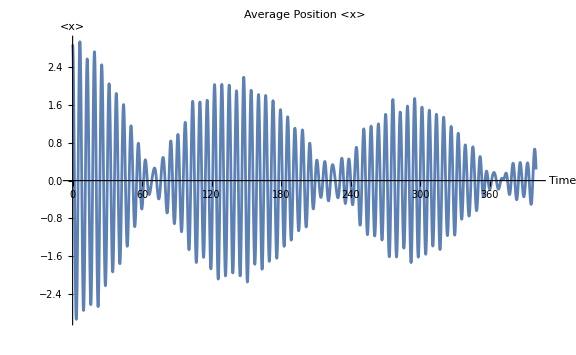

```mathematica
timeEvolutionOperator[t_, h_] := MatrixExp[-I * h * t];
stateVector[t_, i0_, h_] := timeEvolutionOperator[t, h].i0;

(* Compute expectation values *)
EVX[t_]:=ConjugateTranspose[stateVector[t, ψ0, hTotal]].EX.stateVector[t, ψ0, hTotal];
tMax = 400; 

avgPositionPlotQHO = Plot[EVX[t], {t, 0, tMax}, PlotLabel -> "Average Position <x>", AxesLabel -> {"Time", "<x>"}, PlotRange -> Full];
Show[avgPositionPlotQHO, PlotRange -> All, ImageSize -> Large]
```

## applying the TRWA

The heart of the TRWA is the unitary transformation given by .  The value of the parameter  is expressed in terms of a second parameter, , in the paper. We can solve for  by eliminating the parameter, but it’s a bit messy.  and .  We opt for a numerical solution.

```mathematica
eq1 = ξ == ω/(ω + η*Ω);
eq2 = η == Exp[-(g^2/(2*ω^2))*ξ^2];
solution = NSolve[{eq1, eq2}, {ξ, η}, Reals];
xi = ξ /. solution[[1]];
eta = η /. solution[[1]];
```

Now, we consider the transformation to the Hamiltonian whose purpose is to keep the effect of the counter-rotating terms.

```mathematica
S = g/(2ω) * xi * KroneckerProduct[PauliMatrix[3], b† - b];
transformedH = MatrixExp[S].hTotal.MatrixExp[-S];
transformedEX = MatrixExp[S].EX.MatrixExp[-S];
transformedψ0 = MatrixExp[S].ψ0;

transformedEVX[t_]:=ConjugateTranspose[stateVector[t, transformedψ0, transformedH]].transformedEX.stateVector[t, transformedψ0, transformedH];

(*avgPositionPlotQHO = Plot[Re[transformedEVX[t]], {t, 0, tMax}, PlotLabel -> "Average Position <x>", AxesLabel -> {"Time", "<x>"}, PlotRange -> Full];
Show[avgPositionPlotQHO, PlotRange -> All, ImageSize -> Large]*)

(*now we make the approximation*)
(*
transformedH0 = 
1/2 * eta * Ω * SparseArray[KroneckerProduct[PauliMatrix[1], IdentityMatrix[bsize]] + 
KroneckerProduct[IdentityMatrix[2], hQHO]] - 
(g^2)/(4ω) * xi * (2 - xi);

transformedH1 = 
eta * Ω * g/ω * xi * (SparseArray[
(KroneckerProduct[ PauliMatrix[3] + I * PauliMatrix[2], b†]) + 
(KroneckerProduct[ PauliMatrix[3] - I * PauliMatrix[2], b])])

hTRWA = transformedH0 + transformedH1;

TRWAevx[t_] = ConjugateTranspose[stateVector[t, transformedψ0, hTRWA]].transformedEX.stateVector[t, transformedψ0, hTRWA];

avgPositionPlotQHO = Plot[Re[TRWAevx[t]], {t, 0, tMax}, PlotLabel -> "Average Position <x>", AxesLabel -> {"Time", "<x>"}, PlotRange -> Full];
Show[avgPositionPlotQHO, PlotRange -> All, ImageSize -> Large] *)
```

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{0,1},{1,0}},{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}},10,10]].

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{0,1},{1,0}},{{1,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1}},10,10]].

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{0.,1.},{1.,0.}},{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},«4»,{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}},10.,10.]].

KroneckerProduct::rect: Nonrectangular array encountered.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{0.,1.},{1.,0.}},{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},«4»,{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}},10.,10.]].

KroneckerProduct::rect: Nonrectangular array encountered.

General::stop: Further output of KroneckerProduct::rect will be suppressed during this calculation.

SparseArray::list: List expected at position 1 in SparseArray[KroneckerProduct[{{0.,1.},{1.,0.}},{{1.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,1.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,1.,0.,0.,0.,0.,0.,0.,0.},«4»,{0.,0.,0.,0.,0.,0.,0.,1.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,1.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,1.}},10.,10.]].

General::stop: Further output of SparseArray::list will be suppressed during this calculation.

Eigenvalues::eival: Unable to find all roots of the characteristic polynomial.

General::stop: Further output of Eigenvalues::eival will be suppressed during this calculation.